# Blatt 5 - Optimierung der Emittanz im DBA-Lattice

Jonas Neundorf & Jan Skottke

Definiere Konstanten

```mathematica
constants={c-> 3.*10^8, q-> 1.602*10^-19,m-> 0.511*10^-3,r0-> 2.818*10^-15,cq-> 3.8*10^-13};
```

Du kannst η mit “Esc h Esc” schreiben (dann musst du nicht immer “Esc et Esc” benutzten)
Und das geschwungene ℋ kannst du mit “Esc scH Esc” machen.

## Vorbereitungen

#### Berechnung der Dispersionfunktion

Definiere die Matritzen für die Magnete:

```mathematica
mF[f_]:={{1,0,0},{-1/f,1,0},{0,0,1}} (*fokussierender Quad*)
```

```mathematica
mD[s_, ρ_] := {{Cos[s/ρ], ρ*Sin[s/ρ], ρ*(1 - Cos[s/ρ])}, {-1/ρ*Sin[s/ρ], Cos[s/ρ], Sin[s/ρ]}, {0, 0, 1}}(*Dipol*)
```

Definiere Dispersionsfunktionen:

```mathematica
η[s_]:=ρ*(1-Cos[s/ρ])
```

```mathematica
dη[s_]=D[η[s],s];
```

Die Dispersion soll nach durchqueren des DBA sich nicht geändert haben. Aus dieser Bedingung lässt sich die Brennweite bestimmen.

```mathematica
eq={0,0,1}==mD[L,ρ].mF[f].mD[L,ρ].{η[0],dη[0],1}//FullSimplify (*Dispersion nach dem ersten Dipol*)
```

{0,0,1}=={(ρ (-2 f cos((2 L)/ρ)+2 f-2 ρ sin(L/ρ)+ρ sin((2 L)/ρ)))/(2 f),(cos(L/ρ) (2 f sin(L/ρ)+ρ (cos(L/ρ)-1)))/f,1}

```mathematica
focus=Solve[eq,f]//Flatten
```

{f→1/2 ρ tan(L/(2 ρ))}

Diese Brennweite muss der Quadropol haben, damit die Dispersion am Ende wieder bei {0,0,1} ist.

#### Tests

Definieren wir zunächst einige Parameter, die wir für den Test benötigen.

```mathematica
params = {L->5, ρ->600}
```

{L→5,ρ→600}

Die berechnete Brennweite liefert das gewünschte Ergebnis, dass die Dispersion nach dem 2. Dipol wieder bei {0,0,1} ist.

```mathematica
mD[L,ρ].mF[f].mD[L,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{0,0,1}

Dispersion nach dem ersten Dipol:

```mathematica
dispd1=mD[L,ρ].{η[0],dη[0],1}//FullSimplify
```

{ρ-ρ cos(L/ρ),sin(L/ρ),1}

Dispersion nach dem Quadropol und dem zweiten Dipol: (Hier gehen wir nur davon aus, dass der Startpunkt im Quadropol liegt und NICHT im 1. Dipol, da die Dispersion nach dem Quadropol und 2. Dipol ja {η,-dη} sein sollte. Und das ist sie!! :))

```mathematica
dispqd2=mF[f].mD[L,ρ].{η[0],dη[0],1}//.focus//FullSimplify
```

{ρ-ρ cos(L/ρ),-sin(L/ρ),1}

Definieren wir nun η und η’ im gesamten DBA:

```mathematica
fullη[s_] := Piecewise[ {{(mD[s,ρ].{0, 0, 1})[[1]], s <= L},{(mD[s-L, ρ].mF[f].mD[L, ρ].{0, 0, 1})[[1]], L < s≤ 2*L}}]
```

```mathematica
fulldη[s_] := Piecewise[ {{(mD[s,ρ].{0, 0, 1})[[2]], s <= L},{(mD[s-L, ρ].mF[f].mD[L, ρ].{0, 0, 1})[[2]], L < s≤ 2*L}}]
```

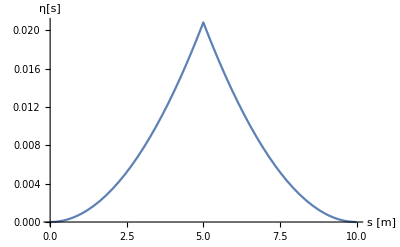

```mathematica
Plot[fullη[s] //.focus //.params, {s, 0, 10}, AxesLabel->{"s [m]", "η[s]"}]
```

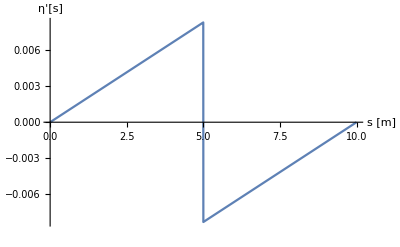

```mathematica
Plot[fulldη[s] //.focus //.params, {s, 0, 10}, AxesLabel-> {"s [m]", "η'[s]"}]
```

#### Berechnung der Twiss Parameter (β-Funktionen)

```mathematica
bmat={{β0,-α0},{-α0,γ0}}
```

(β0 | -α0
-α0 | γ0)

```mathematica
drift[s_]:={{1,s},{0,1}}
```

```mathematica
quad[f_]:={{1,0},{-1/f,1}}
```

Zuerst berechnen wir die Parameter für den ersten Dipol:

```mathematica
twissd1[s_]=drift[s].bmat.Transpose[drift[s]]//FullSimplify
```

(γ0 s^2-2 α0 s+β0 | s γ0-α0
s γ0-α0 | γ0)

Nun zur Berechnung der Twissparameter für den letzten Teil, also für den Quadropol und dem zweiten Dipol: (Kommentar: Wenn ich mich richtig erinnere dann müsste folgendes gelten: B_1 = M * B_0 * M^T(das steht so im Skript) und weiter sollte gelten (das habe ich nicht im Skript gefunden): 
B_2 = M * B_1 * M^T= M * (M * B_0 * M^T) * M^T; wenn das nicht richtig ist, musst du ab hier einiges korrigieren :( )
Jo das stimmt schon, in der Umsetyung war ein Fehler.

```mathematica
twissqd2[s_]=drift[s-L].quad[f].(twissd1[L]).Transpose[drift[s-L].quad[f]] //.focus //FullSimplify
(*(quad[f].bmat.Transpose[quad[f]]).Transpose[drift[s]]//.focus//FullSimplify*)
```

(γ0 s^2-2 α0 s+β0+(4 (L-s) cot(L/(2 ρ)) ((-(L+s) α0+β0+L s γ0) ρ+(L-s) (γ0 L^2-2 α0 L+β0) cot(L/(2 ρ))))/ρ^2 | -α0+s γ0+(2 cot(L/(2 ρ)) ((2 s α0-β0+L (L-2 s) γ0) ρ+2 (s-L) (γ0 L^2-2 α0 L+β0) cot(L/(2 ρ))))/ρ^2
-α0+s γ0+(2 cot(L/(2 ρ)) ((2 s α0-β0+L (L-2 s) γ0) ρ+2 (s-L) (γ0 L^2-2 α0 L+β0) cot(L/(2 ρ))))/ρ^2 | γ0+(4 cot(L/(2 ρ)) ((α0-L γ0) ρ+(γ0 L^2-2 α0 L+β0) cot(L/(2 ρ))))/ρ^2)

```mathematica
β[s_]=Piecewise[{{twissd1[s][[1,1]], s≤ L}, {twissqd2[s][[1,1]], L≤ s≤2*L}}]
```

Piecewise[{{β0+γ0 s^2-2 α0 s, s≤L}, {β0+(4 (L-s) cot(L/(2 ρ)) ((L-s) cot(L/(2 ρ)) (β0+γ0 L^2-2 α0 L)+ρ (β0+α0 (-(L+s))+γ0 L s)))/ρ^2+γ0 s^2-2 α0 s, L≤s≤2 L}}]

```mathematica
α[s_]=Piecewise[{{-twissd1[s][[1,2]], s≤ L}, {-twissqd2[s][[1,2]], L≤ s≤2*L}}]
```

Piecewise[{{α0-γ0 s, s≤L}, {α0-(2 cot(L/(2 ρ)) (2 (s-L) cot(L/(2 ρ)) (β0+γ0 L^2-2 α0 L)+ρ (-β0+γ0 L (L-2 s)+2 α0 s)))/ρ^2-γ0 s, L≤s≤2 L}}]

```mathematica
γ[s_]=Piecewise[{{twissd1[s][[2,2]], s<=L}, {twissqd2[s][[2,2]], L≤ s≤2*L}}]
```

Piecewise[{{γ0, s≤L}, {γ0+(4 cot(L/(2 ρ)) (cot(L/(2 ρ)) (β0+γ0 L^2-2 α0 L)+ρ (α0-γ0 L)))/ρ^2, L≤s≤2 L}}]

#### Berechnung der Funktion ℋ

Als Hinweis: das eigentliche η in der Gleichung (siehe Aufgabenblatt) wird hier durch fullη und η' wird durch fulldη ersetzt. Falls dir ein besserer Name dafür einfällt, kannst du das gerne ändern. :D

```mathematica
ℋ[s_]:=PiecewiseExpand[γ[s]*(fullη[s])^2]+2*PiecewiseExpand[α[s]*fullη[s]*fulldη[s]]+PiecewiseExpand[β[s]*(fulldη[s])^2]
```

## Berechnung und Optimierung der Emittanz

```mathematica
para={ρ-> L/θ,L-> 1.96, θ-> 0.0984,γrel-> 6000/0.511};(*θ->L/ρ*)
```

```mathematica
parastart={γ0-> (1+α0^2)/β0,β0-> 2*√(3/5)*L,α0-> √15}; (*Bei γ0 bin ich mir nicht 100%ig sicher ob man das so machen darf, aber mir ist nichts besseres eingefallen*)
```

#### Die Twiss-Parameter

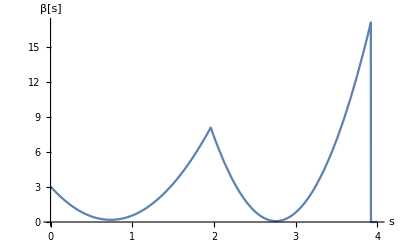

```mathematica
Plot[β[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "β[s]"}] (*keine Ahnung was ich dazu sagen soll oder was mir da auffällt, vielleicht habe ich auch i.wo einen Fehler gemacht, was nicht so unwahrscheinlich ist....*)
```

```mathematica
f//.focus//.para
```

0.490396

Der Verlauf der β-Funktion und insbesondere die Lage der Minima sehen komisch aus. Wir hätten Minima ungefähr im Abstand f vom Quadrupol erwartet, allerdings ist er deutlich größer

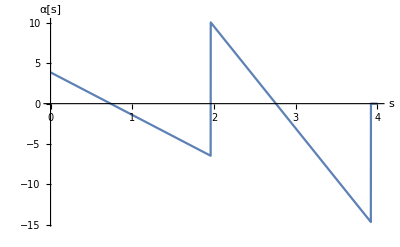

```mathematica
Plot[α[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "α[s]"}]
```

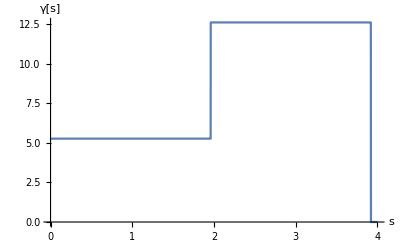

```mathematica
Plot[γ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "γ[s]"}]
```

Da aus den DBA eine periodische Struktur entsteht, sollten die Twiss-Parameter an Anfang und Ende gleich sein -- was sie offensichtlich nicht sind.

#### Die Funktion ℋ

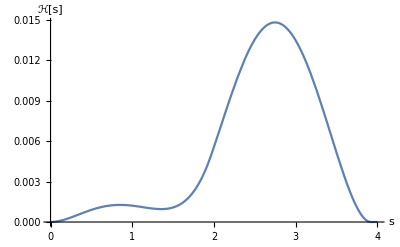

```mathematica
Plot[ℋ[x]//.focus//.parastart//.para, {x, 0, 4}, AxesLabel-> {"s", "ℋ[s]"}]
```

#### Richtige Optimierung

```mathematica
numH[s_]:=ℋ[s]//.focus//.γ0-> (1+α0^2)/β0//.para;//FullSimplify
```

```mathematica
Clear[s]
```

```mathematica
intH=Integrate[numH[s],{s, 0, L//.para}] + Integrate[numH[s], {s, L//.para, 2*L//.para}] //FullSimplify
```

(0.0241915 α0^2+0.0241915)/β0-0.0444697 α0+0.0214466 β0

```mathematica
nsβ=Solve[D[intH,β0]==0,β0]//FullSimplify (*da β0>0 sein soll, muss man die 2. Lösung nehmen*)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{β0→-1.44092×10^-8 √(5.43283×10^15 α0^2+5.43283×10^15)},{β0→1.44092×10^-8 √(5.43283×10^15 α0^2+5.43283×10^15)}}

```mathematica
nsα=Solve[D[intH,α0]==0,α0]//FullSimplify//Flatten
```

{α0→0.919117 β0}

Setzen wir nun diese Parameter ein, um zu gucken was passiert. Wobei, momentan hängen die voneinander ab, das gibt Rekursion bis ins unendliche. Aber wir können ja einfach mal die Rule für α0 als Gleichung auffassen und da dann β0 einsetzen.

```mathematica
αeq = nsα[[1]] //. Rule->Equal //.nsβ[[2,1]]
```

α0==1.32437×10^-8 √(5.43283×10^15 α0^2+5.43283×10^15)

```mathematica
αsol = Solve[αeq, α0] //Flatten
```

{α0→4.49789}

```mathematica
numParams = {γ0-> (1+α0^2)/β0, nsβ[[2,1]], αsol[[1]]}
```

{γ0→(α0^2+1)/β0,β0→1.44092×10^-8 √(5.43283×10^15 α0^2+5.43283×10^15),α0→4.49789}

```mathematica
(*test=Integrate[numH[s]//.para//.ρ-> L/θ,{s,0,2*1.96}∈Reals]//FullSimplify*)
```

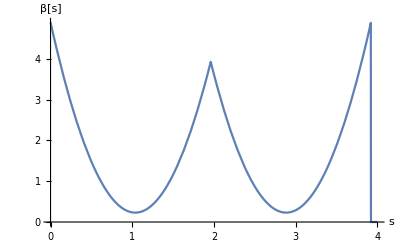

```mathematica
Plot[β[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "β[s]"}]
```

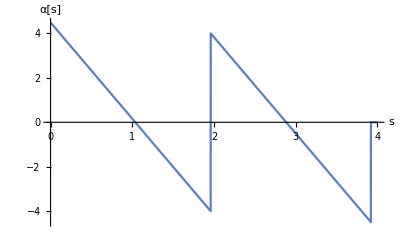

```mathematica
Plot[α[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "α[s]"}]
```

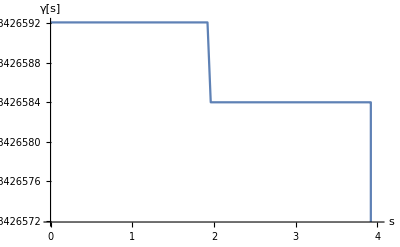

```mathematica
Plot[γ[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "γ[s]"}]
```

Super, α und β sind tatsächlich periodisch. γ nicht, aber da das ja eine Funktion von α und β ist, hat das wohl schon seine Richtigkeit. Plotten wir nun nochmal ℋ

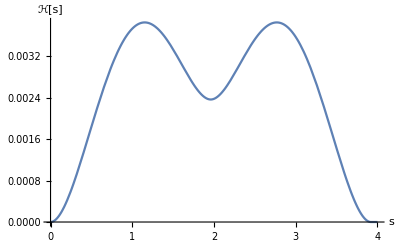

```mathematica
Plot[ℋ[x]//.focus//.numParams//.para, {x, 0, 4}, AxesLabel-> {"s", "ℋ[s]"}]
```

und stellen fest, das auch ℋ auch schön symmetrisch ist.

### Berechnung der Emittanzen und Vergleich

Beginnen wir zunächst mit den kanonischen Parametern.

```mathematica
ϵ = cq * (intH*γrel^2)/(2*L*ρ)
```

```mathematica
Grid[{{"ϵ_kanonisch", ϵ//.parastart //.para}, {"ϵ_optimiert", ϵ //.numParams //.para}, {"ϵ_Formel", 1/(4 √15)*cq *γrel^2*θ^3 //.para //.constants}}]
```